Directory[]
SetDirectory["/home/arianna/Documenti"]
SetDirectory["FeynArts-3.11"]
<< FeynArts`
ResetDirectory[]
SetDirectory["FormCalc-9.9"]
<< FormCalc`

/home/arianna

/home/arianna/Documenti

/home/arianna/Documenti/FeynArts-3.11

FeynArts 3.11 (2 Sep 2019)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

/home/arianna/Documenti

/home/arianna/Documenti/FormCalc-9.9

FormCalc 9.9 (6 Oct 2019)

by Thomas Hahn

# q q̄→μ μ in EW theory: UV divergences

```mathematica
CKM = IndexDelta;
Neglect[MU] = Neglect[MU2] = 0;
Neglect[MM] = Neglect[MM2] = 0;

process ={-F[3, {1}], F[3, {1}]} -> {-F[2, {2}], F[2, {2}]} ;

SetOptions[InsertFields,  Model -> "SMbgf", GenericModel -> "Lorentzbgf",InsertionLevel->{Particles} , Restrictions -> NoLightFHCoupling];

(*SetOptions[InsertFields,  Model -> "SM",InsertionLevel->{Particles}, Restrictions -> NoLightFHCoupling];*)
SetOptions[CalcFeynAmp,PaVeReduce->True];
```

## SMbgf: Feynman rules

Definisco valori di cariche e masse sostituite poi nei passaggi finali

```mathematica
CHARGESZl={QZLl->-1,QZUl->2/3,QZDl->-1/3,I3D->-1/2,I3L->-1/2,I3N->1/2,I3U->1/2}
CHARGESZr={QZLr->-1,QZUr->2/3,QZDr->-1/3}
CHARGES={QL->-1,QU->2/3,QD->-1/3}
MASSES={MU->0,MU2->0,MM->0,MM2->0,S+T+U->0}
```

{QZLl→-1,QZUl→2/3,QZDl→-1/3,I3D→-1/2,I3L→-1/2,I3N→1/2,I3U→1/2}

{QZLr→-1,QZUr→2/3,QZDr→-1/3}

{QL→-1,QU→2/3,QD→-1/3}

{MU→0,MU2→0,MM→0,MM2→0,S+T+U→0}

```mathematica
(*GENERALIZZAZIONE CARICHE/ISOSPIN PER CASO BACKGROUND FIELD METHOD*)
coupling[x_]:=Module[{Mcouplin,chargenuZ,chargelepZ,chargeupZ,chargedownZ,n,m,chargelep,chargedown,chargeup},

Mcouplin=M$CouplingMatrices;
(*____________________________  Z COUPLING  ______________________________*)
(*neutrino*)
chargenuZ[(lhs:C[_. F[1,{__}],_. F[1,{__}],_. V[2]|V[20]])==rhs_]:=
lhs==(rhs/.{

EL->2*I3N*EL
});
chargenuZ[other_]=other;
Mcouplin=chargenuZ/@Mcouplin;

(*lepton*)
chargelepZ[(lhs:C[_. F[2,{__}],_. F[2,{__}],_. V[2]|V[20]])==rhs_]:=
lhs==(rhs/.{
(-1/2+SW^2)IndexDelta[n_,m_]->(I3L-QZLl*SW^2)IndexDelta[n,m],	
(1/2-CW2)IndexDelta[n_,m_]->(I3L-QZLl*SW^2)IndexDelta[n,m], 
(-CW2+SW2)->2*(I3L-QZLl*SW^2),
I->-QZLr*I,
1/2*I->-1/2 QZLr*I
});
chargelepZ[other_]=other;
Mcouplin=chargelepZ/@Mcouplin;

(*q up*)
chargeupZ[(lhs:C[_. F[3,{__}],_. F[3,{__}],_. V[2]|V[20]])==rhs_]:=
lhs==(rhs/.{
(1/2-2/3SW^2)->(I3U-QZUl*SW^2),
(-1+4 CW2) ->6*(I3U-QZUl*SW^2),
-1/3 I*EL->-QZUr/2 I*EL,
-2/3->-QZUl,
-2/3*I->-QZUr*I
});
chargeupZ[other_]=other;
Mcouplin=chargeupZ/@Mcouplin;

(*q down*)
chargedownZ[(lhs:C[_. F[4,{__}],_. F[4,{__}],_. V[2]|V[20]])==rhs_]:=
lhs==(rhs/.{
1/6 I*EL->-QZDr/2 I*EL,
(-1/2+1/3 SW^2)->(I3D-QZDl*SW^2),
(1+2 CW2)->-6*(I3D-QZDl*SW^2),
1/3->-QZDl,
1/3*I->-QZDr*I
});
chargedownZ[other_]=other;
Mcouplin=chargedownZ/@Mcouplin;


(*____________________________  GAMMA COUPLING  ___________________________*)
(*lepton*)
chargelep[(lhs:C[_. F[2,{__}],_. F[2,{__}],_. V[1]|V[10]])==rhs_]:=
lhs==(rhs/.{

I->-QL*I,
1/2*I->-1/2 QL*I
});
chargelep[other_]=other;
Mcouplin=chargelep/@Mcouplin;

(*q up*)
chargeup[(lhs:C[_. F[3,{__}],_. F[3,{__}],_. V[1]|V[10]])==rhs_]:=
lhs==(rhs/.{

-1/3 I*EL->-QU/2 I*EL,
-2/3->-QU,
-2/3*I->-QU*I
});
chargeup[other_]=other;
Mcouplin=chargeup/@Mcouplin;

(*q down*)
chargedown[(lhs:C[_. F[4,{__}],_. F[4,{__}],_. V[1]|V[10]])==rhs_]:=
lhs==(rhs/.{
1/6 I*EL->-QD/2 I*EL,
1/3->-QD,
1/3*I->-QD*I
});
chargedown[other_]=other;
Mcouplin=chargedown/@Mcouplin;

Mcouplin
];
```

```mathematica
InitializeModel["SMbgf",GenericModel->"Lorentzbgf", 
ModelEdit :>{(
M$ClassesDescription=M$ClassesDescription//.{(-Charge)->QL Charge,(2/3Charge)->QU Charge,(-1/3Charge)->QD Charge}),
M$CouplingMatrices=coupling[M$CouplingMatrices]}

];
```

loading generic model file /home/arianna/Documenti/FeynArts-3.11/Models/Lorentzbgf.gen

> $GenericMixing is OFF

generic model {Lorentzbgf} initialized

loading classes model file /home/arianna/Documenti/FeynArts-3.11/Models/SMbgf.mod

> 60 particles (incl. antiparticles) in 24 classes

> $CounterTerms are ON

> 691 vertices

> 334 counterterms of order 1

> 2 counterterms of order 2

classes model {SMbgf} initialized

## Feynman Diagrams

## Tree Level

Excluding 24 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 2 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

Restoring 24 field point(s)

in total: 2 Particles insertions

> Top. 1 aebe/cfdf/ef.m, 0 diagrams

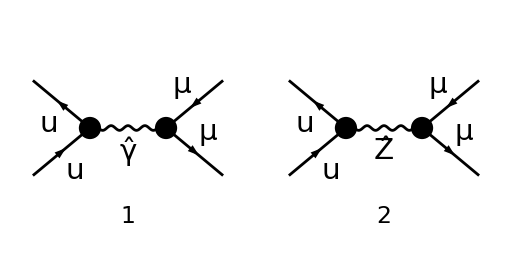

FeynArtsGraphics[][([1] | [2])]

creating amplitudes at level(s) {Particles}

> Top. 1: 2 Particles amplitudes

in total: 2 Particles amplitudes

preparing FORM code in /home/arianna/Documenti/FormCalc-9.9/fc-amp-11.frm

running FORM...

ok

```mathematica
tops = CreateTopologies[0, 2 -> 2];
ins = InsertFields[tops, process];
Paint[ins,ColumnsXRows->{2,1},Numbering->Simple,
SheetHeader->None,ImageSize->{512,256}]
born1=CreateFeynAmp[ins];
born = CalcFeynAmp[born1];
```

## Self Energies

Excluding 24 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 18 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 59 Particles insertions

> Top. 5: 0 Particles insertions

> Top. 6: 0 Particles insertions

Restoring 24 field point(s)

in total: 77 Particles insertions

> Top. 1 aebe/cfdf/egfggg.m, 0 diagrams

> Top. 2 aebe/cfdf/egfhghgh.m, 0 diagrams

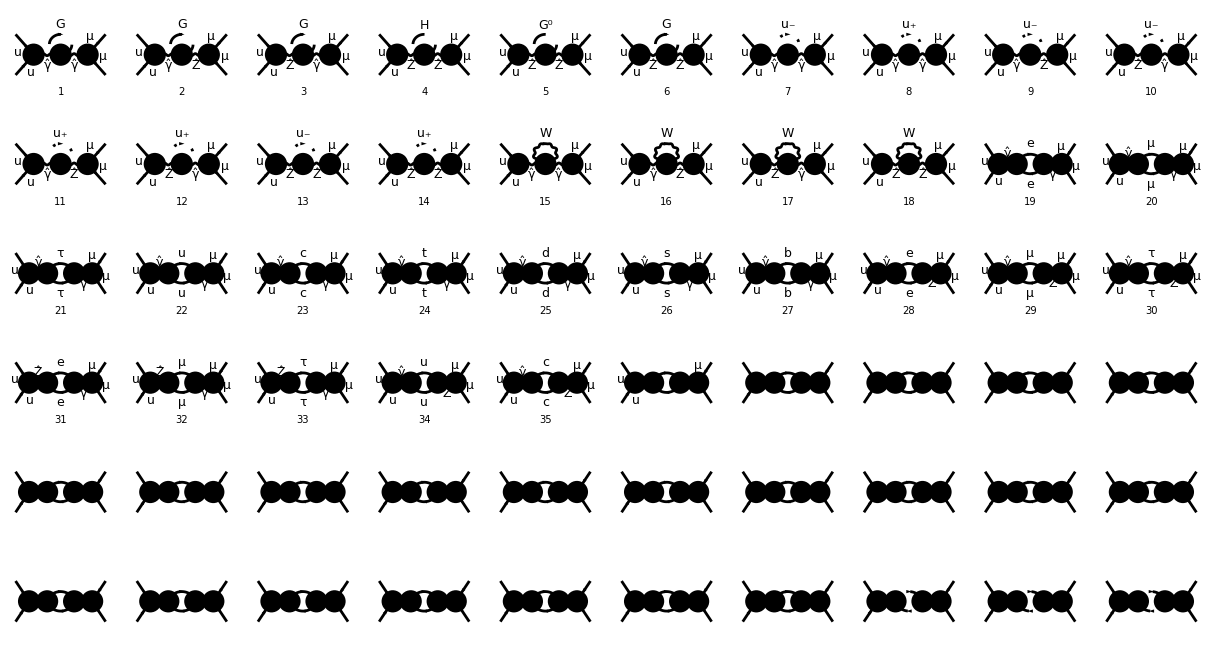

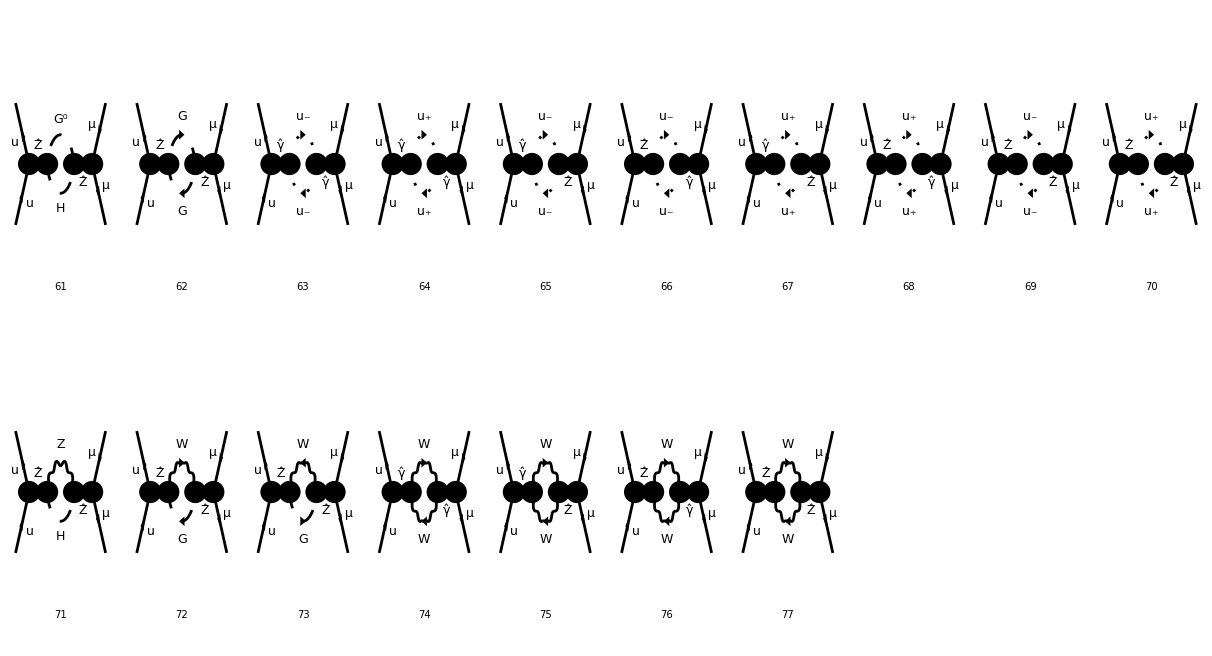

FeynArtsGraphics[][([1] | [2] | [3] | [4] | [5] | [6] | [7] | [8] | [9] | [10]
[11] | [12] | [13] | [14] | [15] | [16] | [17] | [18] | [19] | [20]
[21] | [22] | [23] | [24] | [25] | [26] | [27] | [28] | [29] | [30]
[31] | [32] | [33] | [34] | [35] | [36] | [37] | [38] | [39] | [40]
[41] | [42] | [43] | [44] | [45] | [46] | [47] | [48] | [49] | [50]
[51] | [52] | [53] | [54] | [55] | [56] | [57] | [58] | [59] | [60]),([61] | [62] | [63] | [64] | [65] | [66] | [67] | [68] | [69] | [70]
[71] | [72] | [73] | [74] | [75] | [76] | [77] | Null | Null | Null
Null | Null | Null | Null | Null | Null | Null | Null | Null | Null
Null | Null | Null | Null | Null | Null | Null | Null | Null | Null
Null | Null | Null | Null | Null | Null | Null | Null | Null | Null
Null | Null | Null | Null | Null | Null | Null | Null | Null | Null)]

creating amplitudes at level(s) {Particles}

> Top. 1: 18 Particles amplitudes

> Top. 2: 59 Particles amplitudes

in total: 77 Particles amplitudes

preparing FORM code in /home/arianna/Documenti/FormCalc-9.9/fc-amp-11.frm

running FORM...

ok

```mathematica
tops2 = CreateTopologies[1, 2 -> 2, SelfEnergiesOnly];
ins2 = InsertFields[tops2, process];
ins2 = DiagramSelect[ins2, FreeQ[#, Field[5|6] -> S]&];
Paint[ins2,ColumnsXRows->{10,6},Numbering->Simple,
SheetHeader->None,ImageSize->{1212,656}]
selfff=CreateFeynAmp[ins2];
self = CalcFeynAmp[selfff];
```

```mathematica
selfdiv= UVDivergentPart[self[[1]]];
provaself = Unabbr[SSSSS*selfdiv] ;
```

## Vertices

Excluding 24 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 7 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

> Top. 5: 0 Particles insertions

> Top. 6: 8 Particles insertions

> Top. 7: 0 Particles insertions

> Top. 8: 0 Particles insertions

> Top. 9: 0 Particles insertions

> Top. 10: 0 Particles insertions

> Top. 11: 0 Particles insertions

> Top. 12: 0 Particles insertions

> Top. 13: 0 Particles insertions

> Top. 14: 0 Particles insertions

> Top. 15: 0 Particles insertions

> Top. 16: 0 Particles insertions

> Top. 17: 0 Particles insertions

> Top. 18: 0 Particles insertions

> Top. 19: 0 Particles insertions

> Top. 20: 0 Particles insertions

> Top. 21: 0 Particles insertions

> Top. 22: 0 Particles insertions

> Top. 23: 0 Particles insertions

> Top. 24: 0 Particles insertions

Restoring 24 field point(s)

in total: 15 Particles insertions

> Top. 1 aebe/cfdg/ehfgfhgh.m, 0 diagrams

> Top. 2 aebf/cgdg/ghefehfh.m, 0 diagrams

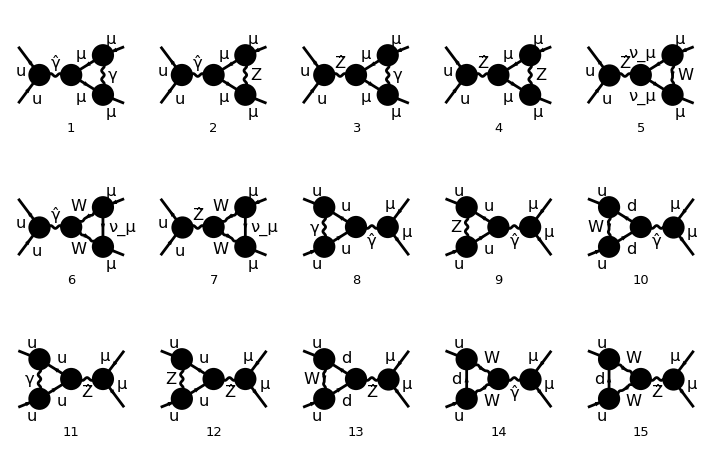

FeynArtsGraphics[][([1] | [2] | [3] | [4] | [5]
[6] | [7] | [8] | [9] | [10]
[11] | [12] | [13] | [14] | [15])]

creating amplitudes at level(s) {Particles}

> Top. 1: 7 Particles amplitudes

> Top. 2: 8 Particles amplitudes

in total: 15 Particles amplitudes

preparing FORM code in /home/arianna/Documenti/FormCalc-9.9/fc-amp-11.frm

running FORM...

ok

```mathematica
tops4 = CreateTopologies[1, 2 -> 2, TrianglesOnly];
ins4 = InsertFields[tops4, process];
ins4 = DiagramSelect[ins4, FreeQ[#, Field[5] -> S]&];
Paint[ins4,ColumnsXRows->{5,3},Numbering->Simple,
SheetHeader->None,ImageSize->{712,456}]
verttt=CreateFeynAmp[ins4];
vert = CalcFeynAmp[verttt];
```

```mathematica
vertdiv = UVDivergentPart[vert[[1]]];
provavert = Unabbr[VVVVV *vertdiv] ;
```

## Boxes

Excluding 24 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

> Top. 5: 0 Particles insertions

> Top. 6: 0 Particles insertions

> Top. 7: 4 Particles insertions

> Top. 8: 5 Particles insertions

> Top. 9: 0 Particles insertions

> Top. 10: 0 Particles insertions

> Top. 11: 0 Particles insertions

> Top. 12: 0 Particles insertions

Restoring 24 field point(s)

in total: 9 Particles insertions

> Top. 1 aebf/cgdh/efegfhgh.m, 0 diagrams

> Top. 2 aebf/cgdh/efehfggh.m, 0 diagrams

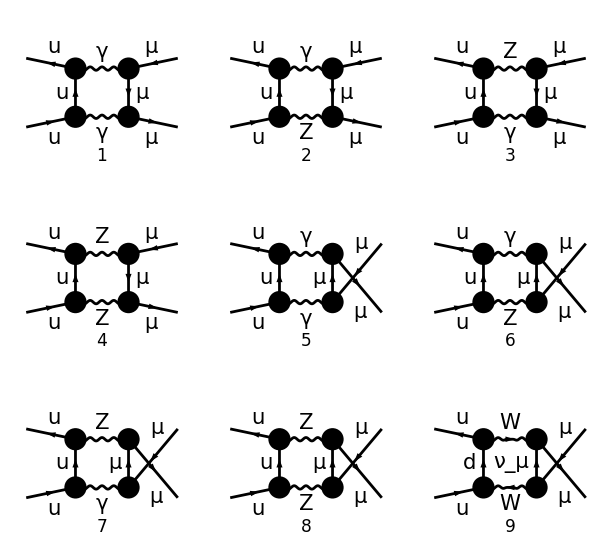

FeynArtsGraphics[][([1] | [2] | [3]
[4] | [5] | [6]
[7] | [8] | [9])]

creating amplitudes at level(s) {Particles}

> Top. 1: 4 Particles amplitudes

> Top. 2: 5 Particles amplitudes

in total: 9 Particles amplitudes

preparing FORM code in /home/arianna/Documenti/FormCalc-9.9/fc-amp-11.frm

running FORM...

ok

```mathematica
tops5 = CreateTopologies[1, 2 -> 2, BoxesOnly];
ins5 = InsertFields[tops5, process];
Paint[ins5,ColumnsXRows->{3,3},Numbering->Simple,
SheetHeader->None,ImageSize->{612,556}]
box1=  CreateFeynAmp[ins5];
box = CalcFeynAmp[box1];
```

### UV divergent part Boxes:

NO UV divergent part in these diagrams.

```mathematica
bboxUV=UVDivergentPart[box[[1]]] //Simplify
```

2 Alfa2 Divergence (2 (Sub568+(Sub608+CW2^2 QL^2 QU^2 Sub661)/(CW2^2 S))+2 QL QU (Sub1146-(8 (MM2+MU2) Sub662)/(CW2 T U (-2 MM2-2 MU2+T+U)))+(-2 Sub658-(Sub675-4 QL QU Sub677)/CW2+(Sub624+Sub678+S Sub681 U-F10 F9 (S+U))/(S SW2^2 U))/T) Mat[SUN1]

```mathematica
provabox=Unabbr[bboxUV];
```

```mathematica
%//.CHARGES //.CHARGESZl //.CHARGESZr //.MASSES //Simplify;
```

```mathematica
%//.MASSES
```

0

## Counterterms (CT)

Excluding 24 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 2 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

> Top. 5: 0 Particles insertions

> Top. 6: 0 Particles insertions

> Top. 7: 2 Particles insertions

> Top. 8: 4 Particles insertions

> Top. 9: 0 Particles insertions

> Top. 10: 0 Particles insertions

Restoring 24 field point(s)

in total: 8 Particles insertions

> Top. 1 aebe/cfdf/ef.m, 0 diagrams

> Top. 2 aebe/cfdf/ef.m, 0 diagrams

> Top. 3 aebe/cfdf/gegf.m, 0 diagrams

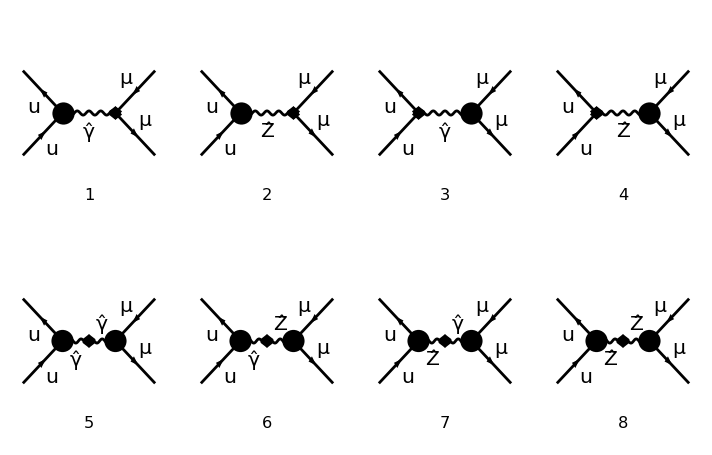

FeynArtsGraphics[][([1] | [2] | [3] | [4]
[5] | [6] | [7] | [8])]

creating amplitudes at level(s) {Particles}

> Top. 1: 2 Particles amplitudes

> Top. 2: 2 Particles amplitudes

> Top. 3: 4 Particles amplitudes

in total: 8 Particles amplitudes

preparing FORM code in /home/arianna/Documenti/FormCalc-9.9/fc-amp-11.frm

running FORM...

ok

```mathematica
tops1 = CreateCTTopologies[1, 2 -> 2,
  ExcludeTopologies -> {TadpoleCTs,WFCorrectionCTs (*loop counterterms*)}];
ins1 = InsertFields[tops1, process];
Paint[ins1,ColumnsXRows->{4,2},Numbering->Simple,
SheetHeader->None,ImageSize->{712,456}]
counter = CreateFeynAmp[ins1];
ct=CalcFeynAmp[counter];
counterterms = Unabbr[ct];
```

### Renormalization Constants (RC)

```mathematica
rc=CalcRenConst[counterterms];
ddd=Table[UVDivergentPart[rc[[1,i]]]//Simplify,{i,1,Length[rc[[1]]]}];
```

dMWsq1

Excluding 24 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 10 Particles insertions

> Top. 2: 18 Particles insertions

Restoring 24 field point(s)

in total: 28 Particles insertions

creating amplitudes at level(s) {Particles}

> Top. 1: 10 Particles amplitudes

> Top. 2: 18 Particles amplitudes

in total: 28 Particles amplitudes

preparing FORM code in /home/arianna/Documenti/FormCalc-9.9/fc-rc-11.frm

running FORM...

ok

dMZsq1

Excluding 24 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 6 Particles insertions

> Top. 2: 20 Particles insertions

Restoring 24 field point(s)

in total: 26 Particles insertions

creating amplitudes at level(s) {Particles}

> Top. 1: 6 Particles amplitudes

> Top. 2: 20 Particles amplitudes

in total: 26 Particles amplitudes

preparing FORM code in /home/arianna/Documenti/FormCalc-9.9/fc-rc-11.frm

running FORM...

ok

dZAA1

Excluding 24 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 4 Particles insertions

> Top. 2: 13 Particles insertions

Restoring 24 field point(s)

in total: 17 Particles insertions

creating amplitudes at level(s) {Particles}

> Top. 1: 4 Particles amplitudes

> Top. 2: 13 Particles amplitudes

in total: 17 Particles amplitudes

preparing FORM code in /home/arianna/Documenti/FormCalc-9.9/fc-rc-11.frm

running FORM...

ok

dZAZ1

dZZZ1

dZfL1[2,2,2]

Excluding 24 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 3 Particles insertions

Restoring 24 field point(s)

in total: 3 Particles insertions

creating amplitudes at level(s) {Particles}

> Top. 1: 3 Particles amplitudes

in total: 3 Particles amplitudes

preparing FORM code in /home/arianna/Documenti/FormCalc-9.9/fc-rc-11.frm

running FORM...

ok

dZfL1[3,1,1]

Excluding 24 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 3 Particles insertions

Restoring 24 field point(s)

in total: 3 Particles insertions

creating amplitudes at level(s) {Particles}

> Top. 1: 3 Particles amplitudes

in total: 3 Particles amplitudes

preparing FORM code in /home/arianna/Documenti/FormCalc-9.9/fc-rc-11.frm

running FORM...

ok

dZfR1[2,2,2]

dZfR1[3,1,1]

## SELF+VERTICES->UV finite

## Vertici

```mathematica
ctvert=CCCCC*ExpandSums[counterterms[[1]]//. {dMWsq1->0,dMZsq1->0, dZZZ1->0,  dZAA1->0, dZAZ1->0}//.ddd];
```

```mathematica
uvvert1 = Collect[ provavert+ctvert, WeylChain[__], FullSimplify];
```

```mathematica
uvvert2= ExpandSums[ uvvert1 ] (*//.{CCCCC->1,VVVVV->1}*)//. MASSES //SMSimplify;
```

```mathematica
uvvert3= Collect[ uvvert2 //.CHARGES//.CHARGESZl//.CHARGESZr , WeylChain[__], SMSimplify]
```

-(52 Alfa2 Divergence MZ2 (CCCCC-VVVVV) (MW2 Den[S,0]+(-MW2+MZ2) Den[S,MZ2]) Mat[SUNT[Col1,Col2]] ((v̇ 1|7|u̇ 4)) ((u2|6|v3)))/(27 MW2^2)+(Alfa2 Divergence (22 MW2+5 MZ2) (CCCCC-VVVVV) (-8 MW2 MZ2 SW2 Den[S,0]-(8 MW2^2-6 MW2 MZ2+MZ2^2) Den[S,MZ2]) Mat[SUNT[Col1,Col2]] ((v̇ 1|6|u̇ 4)) ((u2|7|v3)))/(108 MW2^2 MZ2 SW2^2)-(Alfa2 Divergence (2 MW2+25 MZ2) (CCCCC-VVVVV) (2 MW2 Den[S,0]+(-2 MW2+MZ2) Den[S,MZ2]) Mat[SUNT[Col1,Col2]] ((v̇ 1|7|v3)) ((u̇ 4|6|u2)))/(54 MW2^2 SW2)+(Alfa2 Divergence (10 MW2-37 MZ2) (CCCCC-VVVVV) (4 MW2 Den[S,0]+(-4 MW2+MZ2) Den[S,MZ2]) Mat[SUNT[Col1,Col2]] ((v̇ 1|6|v3)) ((u̇ 4|7|u2)))/(108 MW2^2 SW2)

### Analisi termini vertici+CT con WeylChain

```mathematica
ClearProcess[]
```

```mathematica
provavert1 = Collect[provavert, WeylChain[__], FullSimplify]//.MASSES;
```

```mathematica
provacts1 = Collect[ CCCCC* counterterms[[1]] //. {dMWsq1->0,dMZsq1->0, dZZZ1->0, dZAA1->0, dZAZ1->0}//.ddd, {WeylChain[__],Den[__]},  FullSimplify]//.MASSES;
```

```mathematica
(*DIAGRAMMI CON SOLO gamma E W*)
CalcFeynAmp[Part[verttt,{6,10,14}]][[1]];
UVDivergentPart[%]//Simplify;
Unabbr[%];
ww2=Collect[% , WeylChain[__], Simplify]/.MASSES;
```

preparing FORM code in /home/arianna/Documenti/FormCalc-9.9/fc-amp-11.frm

running FORM...

ok

```mathematica
(*DIAGRAMMI CON SOLO Z E W*)
CalcFeynAmp[Part[verttt,{5,7,13,15}]][[1]];
UVDivergentPart[%]//Simplify;
Unabbr[%];
ww3=Collect[% , WeylChain[__], Simplify]/.MASSES;
```

preparing FORM code in /home/arianna/Documenti/FormCalc-9.9/fc-amp-11.frm

running FORM...

ok

#### termine 1. SOLO CT RIGHT

In questo caso ho correzione di tutti i diagrammi di vertice che non presentano la W , ma solo scambio di fotone/Z : {1,2,3,8,9,4,11,12}.
Spegnendo le cariche dei due bosoni non trovo le correzioni ai diagrammi misti, dove si scambiano entrambi i bosoni (diagrammi:2,3,9,11)

```mathematica
vct1=uvvert1[[1]]/.Conjugate[x_]->x//.MASSES//SMSimplify
```

1/MW2^2 2 Alfa2 Divergence (MW2 (QL^2+QU^2-QZLr^2-QZUr^2)+MZ2 (QZLr^2+QZUr^2)) (CCCCC-VVVVV) (MW2 QL QU Den[S,0]+(-MW2+MZ2) QZLr QZUr Den[S,MZ2]) Mat[SUNT[Col1,Col2]] ((v̇ 1|7|u̇ 4)) ((u2|6|v3))

#### γ

```mathematica
vct1p=uvvert1[[1]]/.{QZLr->0,QZUr->0,QZDr->0} /.Conjugate[x_]->x//.MASSES//Simplify
```

2 Alfa2 Divergence QL QU (QL^2+QU^2) (CCCCC-VVVVV) Den[S,0] Mat[SUNT[Col1,Col2]] ((v̇ 1|7|u̇ 4)) ((u2|6|v3))

#### Z

```mathematica
vct1p=uvvert1[[1]]/.{QL->0,QU->0,QD->0} /.Conjugate[x_]->x//.MASSES//Simplify
```

(2 Alfa2 Divergence QZLr QZUr (QZLr^2+QZUr^2) SW2^2 (CCCCC-VVVVV) Den[S,MZ2] Mat[SUNT[Col1,Col2]] ((v̇ 1|7|u̇ 4)) ((u2|6|v3)))/CW2^2

#### termine 2. SOLO CT LEFT

Qui si avrà anche lo scambio di W (essendo parte left)

```mathematica
vct2=uvvert1[[2]]/.Conjugate[x_]->x//.MASSES//FullSimplify
```

1/(CW2^2 SW2^2)Alfa2 Divergence (CW2 SW2 (2 CCCCC QL QU (CW2+I3L^2+I3U^2+CW2 (QL^2+QU^2) SW2-2 (I3L QZLl+I3U QZUl) SW2+(QZLl^2+QZUl^2) SW2^2)-(CW2 (QL+QD QL-QU+2 QL QU (QL^2+QU^2) SW2)+2 QL QU (I3L^2+I3U^2-2 (I3L QZLl+I3U QZUl) SW2+(QZLl^2+QZUl^2) SW2^2)) VVVVV) Den[S,0]+(2 CCCCC (I3L-QZLl SW2) (I3U-QZUl SW2) (CW2+I3L^2+I3U^2+CW2 (QL^2+QU^2) SW2-2 (I3L QZLl+I3U QZUl) SW2+(QZLl^2+QZUl^2) SW2^2)+(CW2^2 (-I3L+I3U+QZLl SW2-QZUl SW2)+2 (I3L-QZLl SW2) (-I3U+QZUl SW2) (I3L^2+I3U^2-2 (I3L QZLl+I3U QZUl) SW2+(QZLl^2+QZUl^2) SW2^2)+CW2 (-I3N I3U+I3N QZUl SW2+I3D (-I3L+QZLl SW2)+SW2 (I3L-QZLl SW2) (QZDl-2 (QL^2+QU^2) (I3U-QZUl SW2)))) VVVVV) Den[S,MZ2]) Mat[SUNT[Col1,Col2]] ((v̇ 1|6|u̇ 4)) ((u2|7|v3))

```mathematica
vct22=vct2//.{QD QL->2 QU QL+QU-QL,QZDl->QZUl-1,I3N->I3L+1,I3D->I3U-1} //FullSimplify
```

1/(CW2^2 SW2^2)Alfa2 Divergence (2 CW2 QL QU SW2 (CW2+I3L^2+I3U^2+CW2 (QL^2+QU^2) SW2-2 (I3L QZLl+I3U QZUl) SW2+(QZLl^2+QZUl^2) SW2^2) (CCCCC-VVVVV) Den[S,0]+(I3U-QZUl SW2) (2 CCCCC (I3L-QZLl SW2) (CW2+I3L^2+I3U^2+CW2 (QL^2+QU^2) SW2-2 (I3L QZLl+I3U QZUl) SW2+(QZLl^2+QZUl^2) SW2^2)+(CW2^2-2 (I3L-QZLl SW2) (I3L^2+I3U^2-2 (I3L QZLl+I3U QZUl) SW2+(QZLl^2+QZUl^2) SW2^2)+CW2 (-1-2 I3L (1+(QL^2+QU^2) SW2)+QZLl SW2 (1+2 (QL^2+QU^2) SW2))) VVVVV) Den[S,MZ2]) Mat[SUNT[Col1,Col2]] ((v̇ 1|6|u̇ 4)) ((u2|7|v3))

```mathematica
vct22//.(-1-2 I3L (1+(QL^2+QU^2) SW2)+QZLl SW2 (1+2 (QL^2+QU^2) SW2))->-2(I3L-QZLl SW2) (1+ (QL^2+QU^2) SW2)-CW2 //FullSimplify
```

1/(CW2^2 SW2^2)2 Alfa2 Divergence (CW2+I3L^2+I3U^2+CW2 (QL^2+QU^2) SW2-2 (I3L QZLl+I3U QZUl) SW2+(QZLl^2+QZUl^2) SW2^2) (CCCCC-VVVVV) (CW2 QL QU SW2 Den[S,0]+(I3L-QZLl SW2) (I3U-QZUl SW2) Den[S,MZ2]) Mat[SUNT[Col1,Col2]] ((v̇ 1|6|u̇ 4)) ((u2|7|v3))

#### γ

```mathematica
(*Spegnendo le cariche di Z ho correzioni ai diagrammi di scambio di W e fotone {6,10,14} ve. ww2 e con solo scambio di fotone {1,8} *)
```

```mathematica
provavert1[[2]]/.{QZLl->0,QZUl->0,QZDl->0,I3D->0,I3L->0,I3N->0,I3U->0} //Simplify
```

-(Alfa2 Divergence (QL+QD QL-QU+2 QL QU (QL^2+QU^2) SW2) VVVVV Den[S,0] Mat[SUNT[Col1,Col2]] ((v̇ 1|6|u̇ 4)) ((u2|7|v3)))/SW2

```mathematica
provacts1[[2]]/.{QZLl->0,QZUl->0,QZDl->0,I3D->0,I3L->0,I3N->0,I3U->0} /.Conjugate[x_]->x//Simplify
```

(2 Alfa2 CCCCC Divergence QL QU (1+QL^2 SW2+QU^2 SW2) Den[S,0] Mat[SUNT[Col1,Col2]] ((v̇ 1|6|u̇ 4)) ((u2|7|v3)))/SW2

```mathematica
ww2[[1]]//Simplify
```

-(Alfa2 Divergence (QL+QD QL-QU) Den[S,0] Mat[SUNT[Col1,Col2]] ((v̇ 1|6|u̇ 4)) ((u2|7|v3)))/SW2

```mathematica
vct2p=uvvert1[[2]]/.{QZLl->0,QZUl->0,QZDl->0,I3D->0,I3L->0,I3N->0,I3U->0}/.Conjugate[x_]->x//.MASSES//FullSimplify
```

(Alfa2 Divergence (2 CCCCC QL QU (1+(QL^2+QU^2) SW2)-(QL+QD QL-QU+2 QL QU (QL^2+QU^2) SW2) VVVVV) Den[S,0] Mat[SUNT[Col1,Col2]] ((v̇ 1|6|u̇ 4)) ((u2|7|v3)))/SW2

```mathematica
vct2p//.QD QL->2 QU QL+QU-QL//Simplify
```

(2 Alfa2 Divergence QL QU (1+QL^2 SW2+QU^2 SW2) (CCCCC-VVVVV) Den[S,0] Mat[SUNT[Col1,Col2]] ((v̇ 1|6|u̇ 4)) ((u2|7|v3)))/SW2

```mathematica
%//.CHARGES//Simplify
```

-(4 Alfa2 Divergence (9+13 SW2) (CCCCC-VVVVV) Den[S,0] Mat[SUNT[Col1,Col2]] ((v̇ 1|6|u̇ 4)) ((u2|7|v3)))/(27 SW2)

#### Z

```mathematica
(*in modo analogo, spegnendo le cariche del fotone ho correzioni ai diagrammi di scambio di W e Z {5,7,13,15} ved. ww3 e parte con scambio solo di Z {4,12}*)
```

```mathematica
provavert1[[2]]/.{QL->0,QU->0,QD->0}//SMSimplify
```

-1/(MW2^2 MZ2^2 SW2^2)Alfa2 Divergence (MW2^2 MZ2 (I3L MZ2-I3U MZ2-MZ2 (QZLl-QZUl) SW2)+2 (I3L MZ2-MZ2 QZLl SW2) (I3U MZ2-MZ2 QZUl SW2) (I3L^2 MZ2^2+I3U^2 MZ2^2-2 MZ2^2 (I3L QZLl+I3U QZUl) SW2+MZ2^2 (QZLl^2+QZUl^2) SW2^2)+MW2 MZ2 (I3N MZ2 (I3U MZ2+MW2 QZUl-MZ2 QZUl)-MZ2 QZDl (I3L MZ2+MW2 QZLl-MZ2 QZLl) SW2+I3D MZ2 (I3L MZ2-MZ2 QZLl SW2))) VVVVV Den[S,MZ2] Mat[SUNT[Col1,Col2]] ((v̇ 1|6|u̇ 4)) ((u2|7|v3))

```mathematica
vct2z=uvvert1[[2]]/.{QL->0,QU->0,QD->0}/.Conjugate[x_]->x//.MASSES//FullSimplify
```

1/(CW2^2 SW2^2)Alfa2 Divergence (2 CCCCC (I3L-QZLl SW2) (I3U-QZUl SW2) (CW2+I3L^2+I3U^2-2 (I3L QZLl+I3U QZUl) SW2+(QZLl^2+QZUl^2) SW2^2)+(CW2^2 (-I3L+I3U+QZLl SW2-QZUl SW2)+CW2 (-I3D I3L-I3N I3U+I3L QZDl SW2+I3D QZLl SW2+I3N QZUl SW2-QZDl QZLl SW2^2)+2 (I3L-QZLl SW2) (-I3U+QZUl SW2) (I3L^2+I3U^2-2 (I3L QZLl+I3U QZUl) SW2+(QZLl^2+QZUl^2) SW2^2)) VVVVV) Den[S,MZ2] Mat[SUNT[Col1,Col2]] ((v̇ 1|6|u̇ 4)) ((u2|7|v3))

```mathematica
vct2z=vct2z//.{QZDl->QZUl-1,I3N->I3L+1,I3D->I3U-1}//FullSimplify
```

1/(CW2^2 SW2^2)Alfa2 Divergence (I3U-QZUl SW2) (2 CCCCC (I3L-QZLl SW2) (CW2+I3L^2+I3U^2-2 (I3L QZLl+I3U QZUl) SW2+(QZLl^2+QZUl^2) SW2^2)+(CW2^2+CW2 (-1-2 I3L+QZLl SW2)-2 (I3L-QZLl SW2) (I3L^2+I3U^2-2 (I3L QZLl+I3U QZUl) SW2+(QZLl^2+QZUl^2) SW2^2)) VVVVV) Den[S,MZ2] Mat[SUNT[Col1,Col2]] ((v̇ 1|6|u̇ 4)) ((u2|7|v3))

```mathematica
vct2z//.-2 I3L->-2(I3L-QZLl SW2)-CW2 -QZLl SW2+1//FullSimplify
```

-1/(CW2^2 SW2^2)2 Alfa2 Divergence (I3L-QZLl SW2) (-I3U+QZUl SW2) (CW2+I3L^2+I3U^2-2 (I3L QZLl+I3U QZUl) SW2+(QZLl^2+QZUl^2) SW2^2) (CCCCC-VVVVV) Den[S,MZ2] Mat[SUNT[Col1,Col2]] ((v̇ 1|6|u̇ 4)) ((u2|7|v3))

```mathematica
%//.CHARGESZl //SMFullSimplify
```

-(Alfa2 Divergence (2 MW2-MZ2) (4 MW2-MZ2) (26 MW2^2-4 MW2 MZ2+5 MZ2^2) (CCCCC-VVVVV) Den[S,MZ2] Mat[SUNT[Col1,Col2]] ((v̇ 1|6|u̇ 4)) ((u2|7|v3)))/(108 MW2^2 MZ2^2 SW2^2)

#### termine 3. misto RL

```mathematica
vct3=uvvert1[[3]]/.Conjugate[x_]->x//.MASSES//Simplify
```

1/(CW2^2 SW2)Alfa2 Divergence (CW2 QU (CCCCC CW2 QL (1+2 QL^2 SW2+2 QU^2 SW2)+2 CCCCC QL (I3L^2-2 I3L QZLl SW2+(QZLl^2+QZUr^2) SW2^2)+CW2 (1-2 QL^3 SW2-2 QL QU^2 SW2) VVVVV-2 QL (I3L^2-2 I3L QZLl SW2+(QZLl^2+QZUr^2) SW2^2) VVVVV) Den[S,0]+QZUr (-CCCCC (I3L-QZLl SW2) (CW2 (1+2 QL^2 SW2+2 QU^2 SW2)+2 (I3L^2-2 I3L QZLl SW2+(QZLl^2+QZUr^2) SW2^2))+(-CW2^2+2 (I3L-QZLl SW2) (I3L^2-2 I3L QZLl SW2+(QZLl^2+QZUr^2) SW2^2)+CW2 (I3N+2 (QL^2+QU^2) SW2 (I3L-QZLl SW2))) VVVVV) Den[S,MZ2]) Mat[SUNT[Col1,Col2]] ((v̇ 1|7|v3)) ((u̇ 4|6|u2))

```mathematica
vct3//.(1-2 QL^3 SW2-2 QL QU^2 SW2)->(-QL-2 QL^3 SW2-2 QL QU^2 SW2)//.I3N->I3L-QZLl SW2 +CW2//Simplify
```

1/(CW2^2 SW2)Alfa2 Divergence (CW2 (1+2 QL^2 SW2+2 QU^2 SW2)+2 (I3L^2-2 I3L QZLl SW2+(QZLl^2+QZUr^2) SW2^2)) (CCCCC-VVVVV) (CW2 QL QU Den[S,0]+QZUr (-I3L+QZLl SW2) Den[S,MZ2]) Mat[SUNT[Col1,Col2]] ((v̇ 1|7|v3)) ((u̇ 4|6|u2))

#### γ

```mathematica
(*COMESOPRA:Spegnendo le cariche di Z ho correzioni ai diagrammi di scambio di W e fotone {6,10,14} ve. ww2 e con solo scambio di fotone {1,8} *)
```

```mathematica
provavert1[[3]]/.{QZLr->0,QZUr->0,QZDr->0,QZLl->0,QZUl->0,QZDl->0,I3D->0,I3L->0,I3N->0,I3U->0}//Simplify
```

-(Alfa2 Divergence QU (-1+2 QL (QL^2+QU^2) SW2) VVVVV Den[S,0] Mat[SUNT[Col1,Col2]] ((v̇ 1|7|v3)) ((u̇ 4|6|u2)))/SW2

```mathematica
vct3p=uvvert1[[3]]/.{QZLr->0,QZUr->0,QZDr->0,QZLl->0,QZUl->0,QZDl->0,I3D->0,I3L->0,I3N->0,I3U->0}/.Conjugate[x_]->x//.MASSES //Simplify
```

(Alfa2 Divergence QU (CCCCC (QL+2 QL^3 SW2+2 QL QU^2 SW2)+(1-2 QL^3 SW2-2 QL QU^2 SW2) VVVVV) Den[S,0] Mat[SUNT[Col1,Col2]] ((v̇ 1|7|v3)) ((u̇ 4|6|u2)))/SW2

```mathematica
vct3p//.(1-2 QL^3 SW2-2 QL QU^2 SW2)->(-QL-2 QL^3 SW2-2 QL QU^2 SW2)//Simplify
```

(Alfa2 Divergence QL QU (1+2 QL^2 SW2+2 QU^2 SW2) (CCCCC-VVVVV) Den[S,0] Mat[SUNT[Col1,Col2]] ((v̇ 1|7|v3)) ((u̇ 4|6|u2)))/SW2

```mathematica
%/.CHARGES
```

-(2 Alfa2 Divergence (1+(26 SW2)/9) (CCCCC-VVVVV) Den[S,0] Mat[SUNT[Col1,Col2]] ((v̇ 1|7|v3)) ((u̇ 4|6|u2)))/(3 SW2)

#### Z

```mathematica
(*COMESOPRA: spegnendo le cariche del fotone ho correzioni ai diagrammi di scambio di W e Z {5,7,13,15} ved. ww3 e parte con scambio solo di Z {4,12}*)
```

```mathematica
provavert1[[3]]/.{QL->0,QU->0,QD->0}//Simplify
```

1/(CW2^2 SW2)Alfa2 Divergence QZUr (-CW2^2+CW2 I3N+2 (I3L-QZLl SW2) (I3L^2-2 I3L QZLl SW2+(QZLl^2+QZUr^2) SW2^2)) VVVVV Den[S,MZ2] Mat[SUNT[Col1,Col2]] ((v̇ 1|7|v3)) ((u̇ 4|6|u2))

```mathematica
vct3z=uvvert1[[3]]/.{QL->0,QU->0,QD->0}/.Conjugate[x_]->x//.MASSES //Simplify
```

-1/(CW2^2 SW2)Alfa2 Divergence QZUr (CCCCC (I3L-QZLl SW2) (CW2+2 (I3L^2-2 I3L QZLl SW2+(QZLl^2+QZUr^2) SW2^2))+(CW2^2-CW2 I3N-2 (I3L-QZLl SW2) (I3L^2-2 I3L QZLl SW2+(QZLl^2+QZUr^2) SW2^2)) VVVVV) Den[S,MZ2] Mat[SUNT[Col1,Col2]] ((v̇ 1|7|v3)) ((u̇ 4|6|u2))

```mathematica
vct3z//.I3N->I3L-QZLl SW2 +CW2//Simplify
```

1/(CW2^2 SW2)Alfa2 Divergence QZUr (-I3L+QZLl SW2) (CW2+2 (I3L^2-2 I3L QZLl SW2+(QZLl^2+QZUr^2) SW2^2)) (CCCCC-VVVVV) Den[S,MZ2] Mat[SUNT[Col1,Col2]] ((v̇ 1|7|v3)) ((u̇ 4|6|u2))

```mathematica
%/.CHARGESZl/.CHARGESZr //SMSimplify
```

-(Alfa2 Divergence (52 MW2^2-86 MW2 MZ2+MZ2^2 (61-36 SW2)) (-1+2 SW2) (CCCCC-VVVVV) Den[S,MZ2] Mat[SUNT[Col1,Col2]] ((v̇ 1|7|v3)) ((u̇ 4|6|u2)))/(54 MW2^2 SW2)

#### termine 4. misto RL

```mathematica
vct4=uvvert1[[4]]/.Conjugate[x_]->x//.MASSES//FullSimplify
```

1/(CW2^2 SW2)Alfa2 Divergence (CW2 QL (CCCCC QU (CW2+2 CW2 (QL^2+QU^2) SW2+2 (I3U^2-2 I3U QZUl SW2+(QZLr^2+QZUl^2) SW2^2))-(CW2 (1+QD+2 QU (QL^2+QU^2) SW2)+2 QU (I3U^2-2 I3U QZUl SW2+(QZLr^2+QZUl^2) SW2^2)) VVVVV) Den[S,0]+QZLr (-CCCCC (I3U-QZUl SW2) (CW2+2 CW2 (QL^2+QU^2) SW2+2 (I3U^2-2 I3U QZUl SW2+(QZLr^2+QZUl^2) SW2^2))+(CW2^2+2 (I3U-QZUl SW2) (I3U^2-2 I3U QZUl SW2+(QZLr^2+QZUl^2) SW2^2)+CW2 (I3D-QZDl SW2+2 (QL^2+QU^2) SW2 (I3U-QZUl SW2))) VVVVV) Den[S,MZ2]) Mat[SUNT[Col1,Col2]] ((v̇ 1|6|v3)) ((u̇ 4|7|u2))

```mathematica
vct4//.(1+QD)->QU//.{I3D-QZDl SW2->I3U-QZUl SW2-CW2 ,QZDl->QZUl-1}//FullSimplify
```

1/(CW2^2 SW2)Alfa2 Divergence (CW2+2 CW2 (QL^2+QU^2) SW2+2 (I3U^2-2 I3U QZUl SW2+(QZLr^2+QZUl^2) SW2^2)) (CCCCC-VVVVV) (CW2 QL QU Den[S,0]+QZLr (-I3U+QZUl SW2) Den[S,MZ2]) Mat[SUNT[Col1,Col2]] ((v̇ 1|6|v3)) ((u̇ 4|7|u2))

#### γ

```mathematica
(*COMESOPRA:Spegnendo le cariche di Z ho correzioni ai diagrammi di scambio di W e fotone {6,10,14} ve. ww2 e con solo scambio di fotone {1,8} *)
```

```mathematica
provavert1[[4]]/.{QZLr->0,QZUr->0,QZDr->0,QZLl->0,QZUl->0,QZDl->0,I3D->0,I3L->0,I3N->0,I3U->0}//Simplify
```

-(Alfa2 Divergence QL (1+QD+2 QU (QL^2+QU^2) SW2) VVVVV Den[S,0] Mat[SUNT[Col1,Col2]] ((v̇ 1|6|v3)) ((u̇ 4|7|u2)))/SW2

```mathematica
vct4p=uvvert1[[4]]/.{QZLr->0,QZUr->0,QZDr->0,QZLl->0,QZUl->0,QZDl->0,I3D->0,I3L->0,I3N->0,I3U->0}/.Conjugate[x_]->x//.MASSES//SMFullSimplify
```

-1/(MZ2 SW2)Alfa2 Divergence QL (2 CCCCC MW2 QU (QL^2+QU^2)-CCCCC MZ2 QU (1+2 QL^2+2 QU^2)-2 MW2 QU (QL^2+QU^2) VVVVV+MZ2 (1+QD+2 QU (QL^2+QU^2)) VVVVV) Den[S,0] Mat[SUNT[Col1,Col2]] ((v̇ 1|6|v3)) ((u̇ 4|7|u2))

```mathematica
(*nei ct non è presente la carica QD,usando le proprietà delle cariche numeriche si trova la semplificazione sse si esegue la sostituzione: *)
```

```mathematica
vct4p//.QD->QU-1//Simplify
```

(Alfa2 Divergence QL QU (-2 MW2 (QL^2+QU^2)+MZ2 (1+2 QL^2+2 QU^2)) (CCCCC-VVVVV) Den[S,0] Mat[SUNT[Col1,Col2]] ((v̇ 1|6|v3)) ((u̇ 4|7|u2)))/(MZ2 SW2)

```mathematica
%/.CHARGES
```

-(2 Alfa2 Divergence (-(26 MW2)/9+(35 MZ2)/9) (CCCCC-VVVVV) Den[S,0] Mat[SUNT[Col1,Col2]] ((v̇ 1|6|v3)) ((u̇ 4|7|u2)))/(3 MZ2 SW2)

#### Z

```mathematica
(*COMESOPRA: spegnendo le cariche del fotone ho correzioni ai diagrammi di scambio di W e Z {5,7,13,15} ved. ww3 e parte con scambio solo di Z {4,12}*)
```

```mathematica
provavert1[[4]]/.{QL->0,QU->0,QD->0}//Simplify
```

1/(CW2^2 SW2)Alfa2 Divergence QZLr (CW2^2+CW2 (I3D-QZDl SW2)+2 (I3U-QZUl SW2) (I3U^2-2 I3U QZUl SW2+(QZLr^2+QZUl^2) SW2^2)) VVVVV Den[S,MZ2] Mat[SUNT[Col1,Col2]] ((v̇ 1|6|v3)) ((u̇ 4|7|u2))

```mathematica
vct4z=uvvert1[[4]]/.{QL->0,QU->0,QD->0}/.Conjugate[x_]->x //.MASSES//FullSimplify
```

1/(CW2^2 SW2)Alfa2 Divergence QZLr (-CCCCC (I3U-QZUl SW2) (CW2+2 (I3U^2-2 I3U QZUl SW2+(QZLr^2+QZUl^2) SW2^2))+(CW2^2+CW2 (I3D-QZDl SW2)+2 (I3U-QZUl SW2) (I3U^2-2 I3U QZUl SW2+(QZLr^2+QZUl^2) SW2^2)) VVVVV) Den[S,MZ2] Mat[SUNT[Col1,Col2]] ((v̇ 1|6|v3)) ((u̇ 4|7|u2))

```mathematica
vct4z//.{I3D-QZDl SW2->I3U-QZUl SW2-CW2,QZDl->QZUl-1}//FullSimplify
```

1/(CW2^2 SW2)Alfa2 Divergence QZLr (-I3U+QZUl SW2) (CW2+2 (I3U^2-2 I3U QZUl SW2+(QZLr^2+QZUl^2) SW2^2)) (CCCCC-VVVVV) Den[S,MZ2] Mat[SUNT[Col1,Col2]] ((v̇ 1|6|v3)) ((u̇ 4|7|u2))

```mathematica
%/.CHARGESZr /.CHARGESZl //SMSimplify
```

(Alfa2 Divergence (4 MW2-MZ2) (52 MW2^2-62 MW2 MZ2+37 MZ2^2) (CCCCC-VVVVV) Den[S,MZ2] Mat[SUNT[Col1,Col2]] ((v̇ 1|6|v3)) ((u̇ 4|7|u2)))/(108 MW2^2 MZ2 SW2)

## Self-energies

```mathematica
ctself=CCCCC*ExpandSums[counterterms[[1]]//.{dZfL1[__]->0,Conjugate[dZfL1[__]]->0,dZfR1[__]->0,Conjugate[dZfR1[__]]->0}//.ddd] ;
```

```mathematica
uvself1=Collect[ provaself+ctself, WeylChain[__], Simplify];
```

```mathematica
uvself2=ExpandSums[ uvself1 ] (*//.{CCCCC->1,SSSSS->1}*)/. MASSES   //SMSimplify;
```

$Aborted

```mathematica
uvself3=Collect[ uvself2, WeylChain[__], SMSimplify];
```

```mathematica
uvself3//.{CCCCC->1,SSSSS->1}//.CHARGES//.CHARGESZl//.CHARGESZr //SMSimplify
```

0

## Vertici+Self

```mathematica
ct1=ExpandSums[counterterms[[1]]//.ddd] ;
```

```mathematica
c2=Collect[ provavert+provaself+ct1, WeylChain[__], Simplify];
```

```mathematica
c3=ExpandSums[ c2 ] //.{CCCCC->1,SSSSS->1,VVVVV->1}/. MASSES //.CHARGES//.CHARGESZl//.CHARGESZr  //SMSimplify
```

1/(108 MW2^2 MZ2^2 S SW2^2)Alfa2 Divergence (MW2-CW2 MZ2) Den[S,MZ2] Mat[SUNT[Col1,Col2]] ((-16 MW2^3 (18 MZ2+31 S)+72 MW2^2 MZ2 (MZ2 (3+4 SW2)+S (15+8 SW2))-36 MW2 MZ2^2 (MZ2 (3-2 SW2+8 SW2^2)+S (27-4 SW2+16 SW2^2))+MZ2^3 (18 MZ2 (1-2 SW2+4 SW2^2)+S (37-72 SW2+144 SW2^2))-256 (MC2+MT2) MW2 MZ2^2 S SW2^2 Den[S,0]) ((v̇ 1|6|u̇ 4)) ((u2|7|v3))+8 MZ2 SW2 (MW2^2 (52 MZ2-64 S)-2 MW2 MZ2 (25 MZ2-7 S+18 MZ2 SW2+36 S SW2)+MZ2^2 (MZ2+2 S) (25-18 SW2+36 SW2^2)+8 (MC2+MT2) MW2 (4 MW2-MZ2) S Den[S,0]) ((v̇ 1|7|v3)) ((u̇ 4|6|u2))+Den[S,MZ2] (24 MZ2^2 S (8 ME2 (3 MW2-4 MZ2)+8 ML2 (3 MW2-4 MZ2)-8 MB2 MZ2-8 MD2 MZ2-8 MS2 MZ2+22 MW2 MZ2-41 MZ2^2-22 MW2 S+41 MZ2 S) SW2^2 ((v̇ 1|7|u̇ 4)) ((u2|6|v3))+3 (176 MW2^3-460 MW2^2 MZ2+268 MW2 MZ2^2-41 MZ2^3) (MZ2-S) S ((v̇ 1|6|u̇ 4)) ((u2|7|v3))-2 MZ2 SW2 (2 (3 MH2^2 MZ2^2+3 MZ2^4+153 MZ2^3 S+2 MZ2^2 (12 MB2-32 MC2+12 MD2+12 ME2+12 ML2+12 MS2-32 MT2-150 MW2-51 S) S-6 MH2 MZ2^2 (MZ2+S)-4 MW2^2 S (16 MC2+16 MT2-36 MW2+33 S)+4 MW2 MZ2 S (-12 MB2+32 MC2-12 MD2-12 ME2-12 ML2-12 MS2+32 MT2+21 MW2+78 S)) ((v̇ 1|7|v3)) ((u̇ 4|6|u2))-3 (4 MW2-MZ2) S (8 MB2 MZ2+8 MD2 MZ2+8 MS2 MZ2-22 MW2 MZ2+41 MZ2^2+22 MW2 S-41 MZ2 S) ((v̇ 1|6|v3)) ((u̇ 4|7|u2)))))

```mathematica
c4= Collect[ c3, WeylChain[__], SMSimplify]
```

0

## tot (vert+self+boxes+ct)

```mathematica
ctot=Collect[ provavert+provaself+ct1+provabox  //.{CCCCC->1,SSSSS->1,VVVVV->1}/. MASSES //.CHARGES//.CHARGESZl//.CHARGESZr, WeylChain[__], Simplify];
```

```mathematica
ctot2=ExpandSums[ ctot ]   //SMSimplify;
```

```mathematica
ctot3= Collect[ ctot2, WeylChain[__], SMSimplify]
```

-(32 Alfa2 Divergence MZ2^2 SW2^2 (S^2 (T-3 U)+S (2 T^2-4 T U-3 U^2)+T (T^2-T U-2 U^2)) Mat[SUNT[Col1,Col2]] ((v̇ 1|7|u̇ 4)) ((u2|6|v3)))/(9 MW2^2 S T (S+T) U)-1/(18 MW2^2 MZ2^2 S SW2^2 T (S+T) U)Alfa2 Divergence (64 MW2^4 (S^2 (T-3 U)+S (2 T^2-4 T U-3 U^2)+T (T^2-T U-2 U^2))-96 MW2^3 MZ2 (S^2 (T-3 U)+S (2 T^2-4 T U-3 U^2)+T (T^2-T U-2 U^2))-12 MW2 MZ2^3 (S^2 (T-3 U)+S (2 T^2-4 T U-3 U^2)+T (T^2-T U-2 U^2))+MZ2^4 (S^2 (T-3 U)+S (2 T^2-4 T U-3 U^2)+T (T^2-T U-2 U^2))+4 MW2^2 MZ2^2 (S^2 (13 T-48 U)+S (26 T^2-61 T U-48 U^2)+13 T (T^2-T U-2 U^2))) Mat[SUNT[Col1,Col2]] ((v̇ 1|6|u̇ 4)) ((u2|7|v3))+(8 Alfa2 Divergence (-2 MW2+MZ2)^2 (4 S+3 T) (S+T+U) Mat[SUNT[Col1,Col2]] ((v̇ 1|7|v3)) ((u̇ 4|6|u2)))/(9 MW2^2 S T (S+T))+(2 Alfa2 Divergence (-4 MW2+MZ2)^2 (4 S+3 T) (S+T+U) Mat[SUNT[Col1,Col2]] ((v̇ 1|6|v3)) ((u̇ 4|7|u2)))/(9 MW2^2 S T (S+T))-1/(9 MW2^2 S T (S+T) U (T+U))4 Alfa2 Divergence (S+T+U) (2 MZ2^2 (4 S+3 T) (T+U)+MW2^2 (38 S T+30 T^2+30 S U+22 T U)-MW2 MZ2 (33 S T+25 T^2+31 S U+23 T U)) Mat[SUNT[Col1,Col2]] ((v̇ 1|7,k[3]|u2)) ((u̇ 4|6,k[1]|v3))-(8 Alfa2 Divergence (S+T+U) (2 MW2^2 T (S+T)-MW2 MZ2 SW2 (S+T) (T-U)+4 MZ2^2 SW2^2 (4 S+3 T) (T+U)) Mat[SUNT[Col1,Col2]] ((v̇ 1|7,k[3]|u2)) ((u̇ 4|7,k[1]|v3)))/(9 MW2^2 S T (S+T) U (T+U))+((v̇ 1|6,k[3]|u2)) (-1/(18 MW2^2 MZ2^2 S SW2^2 T (S+T) U (T+U))Alfa2 Divergence (MZ2^4 (4 S+3 T) (T+U) (S+T+U)+16 MW2^4 (S^2 (19 T+15 U)+T (15 T^2+26 T U+11 U^2)+S (34 T^2+45 T U+15 U^2))-2 MW2 MZ2^3 (S^2 (25 T+23 U)+T (19 T^2+36 T U+17 U^2)+S (44 T^2+65 T U+23 U^2))-4 MW2^3 MZ2 (S^2 (119 T+89 U)+5 T (19 T^2+32 T U+13 U^2)+S (214 T^2+273 T U+89 U^2))+2 MW2^2 MZ2^2 (5 S^2 (29 T+23 U)+T (101 T^2+172 T U+71 U^2)+S (246 T^2+331 T U+115 U^2))) Mat[SUNT[Col1,Col2]] ((u̇ 4|6,k[1]|v3))-1/(9 MW2^2 S T (S+T) U (T+U))2 Alfa2 Divergence (S+T+U) (MZ2^2 (4 S+3 T) (T+U)-MW2 MZ2 (33 S T+25 T^2+31 S U+23 T U)+MW2^2 (76 S T+60 T^2+60 S U+44 T U)) Mat[SUNT[Col1,Col2]] ((u̇ 4|7,k[1]|v3)))

```mathematica
ctot3//.MASSES//.S->-T-U//Simplify
```

0